# Problem Set 1 OPTI 586 Prof. Russell Chipman

Assigned Aug. 26, 2021
Due Wed. Sep. 1, 2021 5:00 pm
Submit to D2L as a Mathematica notebooks. Materials not in Mathematica can also be uploaded.

Reading Assignments: 
	Polarized Light and Optical Systems: Chapt. 1 and Chapt. 2-2.11
	An Elementary Introduction to the Wolfram Language, S. Wolfram, Chapters 1-26
available online
https://www.wolfram.com/language/elementary-introduction/2nd-ed/index.html

Instructions will be sent soon on obtaining Polaris-M polarization software from Airy Optics. 
Questions can be directed to Morgan Harlan at engineeringsupport@airyoptics.com.

Problem 1-8	Quickie Mathematica Problems

Work the following problems from https://www.wolfram.com/language/elementary-introduction/2nd-ed/
10 points each

1.	Use Range, Reverse and Join to create the list {1, 2, 3, 4, 4, 3, 2, 1}. 5.2
2.	Make a bar chart of of the first 10 squares. 6.6
3.	Make a table of the values of n^3 for n from 10 to 20.  6.2
4.	Make a plot of the first 10 squares, starting at 1. 5.3
5.	Make a red, yellow, green column (“traffic light”).  7.2
6.	Make a list whose elements are disks with hues varying from 0 to 1 in steps of 0.1.  8.4
7.	Use ImageAdd to add an image of a Poincare Sphere from the internet to an image of a disk.  10.12 
8.	Use Range and a pure function to create a list of the first 20 squares.  26.1

```mathematica
Problem 1
```

```mathematica
A = Range[1,4]; B = Reverse[A]; C = Join[A,B]
```

Set::wrsym: Symbol C is Protected.

{1,2,3,4,4,3,2,1}

```mathematica
Problem 2
```

{2,4,8,16,32,64,128,256,512,1024}

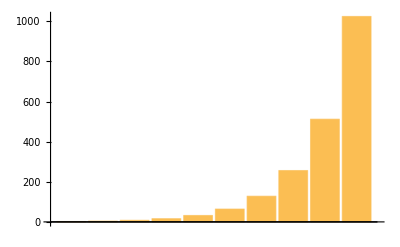

```mathematica
sq = Table[2^n,{n,10}]
BarChart[sq]
```

```mathematica
Problem 3
```

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

```mathematica
Problem 4
```

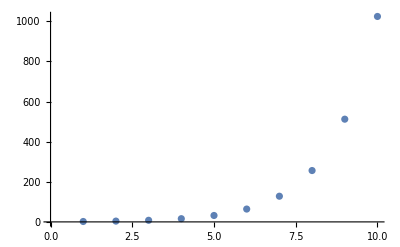

```mathematica
ListPlot[sq]
```

```mathematica
Problem 5
```

```mathematica
trafficlight = {{Red},{Yellow},{Green}}
```

{{RGBColor[1, 0, 0]},{RGBColor[1, 1, 0]},{RGBColor[0, 1, 0]}}

```mathematica
Problem 6
```


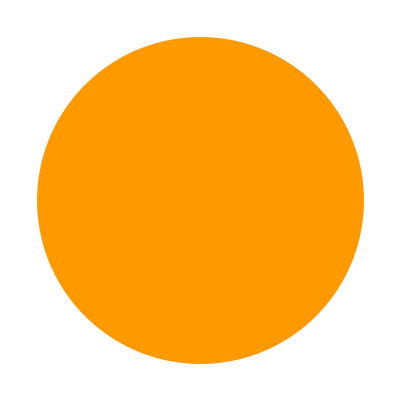
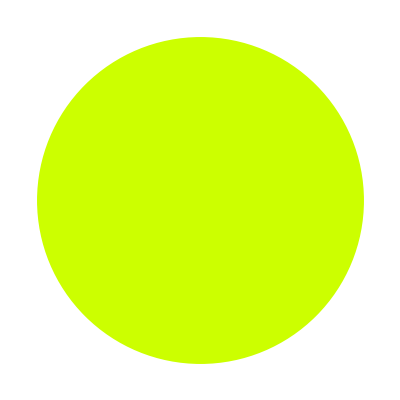
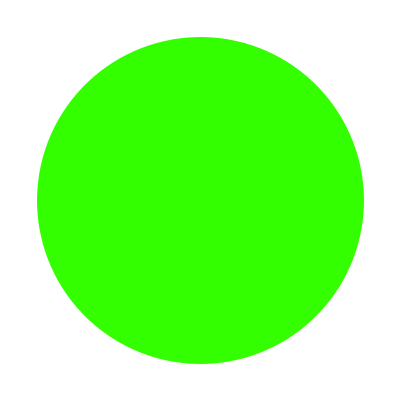
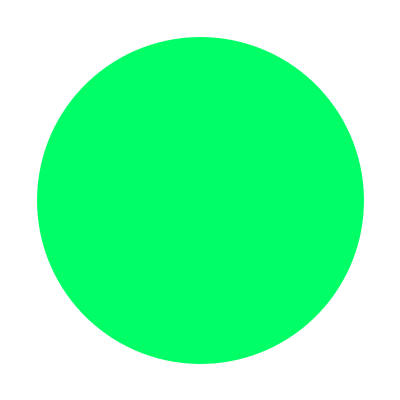
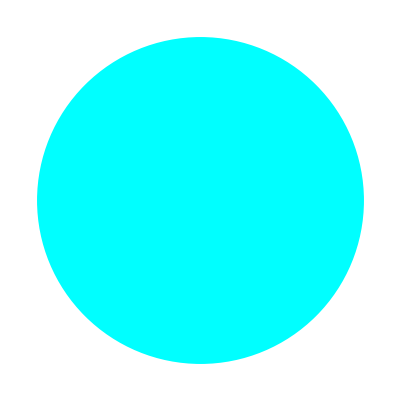
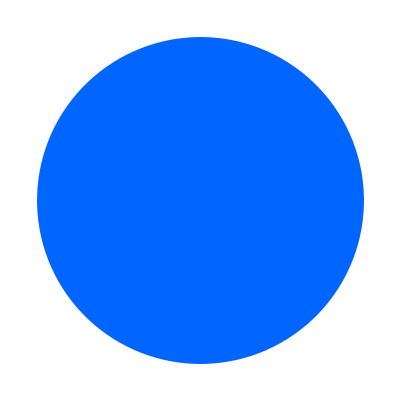
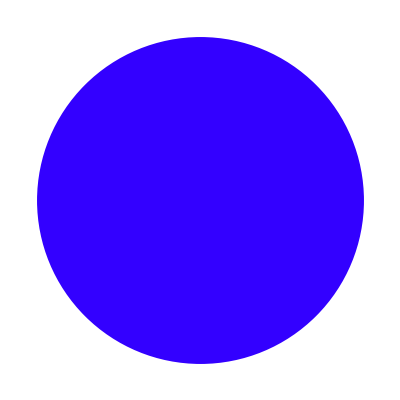
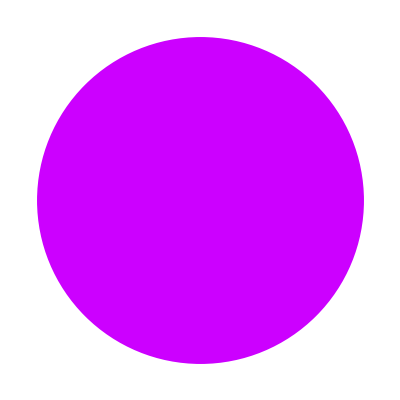
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dlist = Table[Graphics[Style[Disk[],Hue[n]]],{n,0,1,0.1}]
```

```mathematica
Problem 7 -  Image from : "https://spie.org/Images/Graphics/Publications/FG05_P10-11_f3.jpg"
```

```mathematica
ImageAdd[-Graphics-,Part[dlist,5]]
```

-Graphics-

```mathematica
Problem 8
```

```mathematica
f = #^2 &
inargs = Table[n,{n,1,20}]
sqs = f[inargs]
```

#1^2&

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

## Problem 9 Contrast Ratio 10 points

### Contrast ratio C for a polarizer is defined as the ratio of intensity transmittances C=T_max/T_min. Polarization dependent loss is the contrast ratio expressed in decibels, PDL=10 Log[10,T_max/T_min]. Mathematica definition of Log. a. Find an expression for the diattenuation as a function of the contrast ratio. b. When the diattenuation is 0.999, what is the contrast ratio? c. When the diattenuation is 0.999, what is the PDL? d. Show that the PDL for transmission through a series of polarizers with aligned transmission axes is additive, PDL = PDL_1+PDL_2+PDL_3+… . Assume T_(max,1),T_(max,2),T_(max,3), … and T_(min,1),T_(min,2),T_(min,3), … .

```mathematica
Problem 9a
```

```mathematica
C = Subscript[T, max]/Subscript[T, min] ; D = (Subscript[T, max]-Subscript[T, min])/(Subscript[T, max]+ Subscript[T, min])
D = (Subscript[CT, min]-Subscript[T, min])/(Subscript[CT, min]+ Subscript[T, min]) = (C-1)/(C+1)
DC + D = C-1
DC - C = -1-D
C = (1+D)/(1-D)
```

```mathematica
Problem 9b
```

```mathematica
diat = (#-1)/(#+1) &
cont = (1+#)/(1-#) &
cont[0.999]
```

(#1-1)/(#1+1)&

(1+#1)/(1-#1)&

1999.

```mathematica
C[0.999]
```

```mathematica
Problem 9c
```

```mathematica
PDL = 10Log[10,#] &
PDL[cont[0.999]]
```

10 Log[10,#1]&

33.0081

## Problem 10 Sequence of polarizers 10 points

### Malus’s Law states that when a perfect linear polarizer is placed in a linearly polarized beam, the fraction of light transmitted is F=cos^2 θ, where θ is the angle between the incident polarization and the transmission axis of the polarizer.

```mathematica
PolPlot[α_,β_]:=
Graphics3D[{
Opacity[1],Brown,Arrow[Tube[{{0,0,-1},{0,0,5}},0.02]],
Opacity[1],Brown,Arrowheads[0.02*{-1,1}],
Arrow[Tube[{0.7*-{Cos[α °],Sin[α °],0},0.7*{Cos[α °],Sin[α °],0}},0.02]],
Opacity[0.3],Gray,Cuboid[{-1,-1,1.98},{1,1,2}],
Opacity[1],Gray,Arrowheads[0.02*{0,0}],
Arrow[Tube[{0.3*-{Cos[β °],Sin[β °],0}+{0,-0.6,2},0.3*{Cos[β °],Sin[β °],0}+{0,-0.6,2}},0.02]],
Opacity[1],Brown,Arrowheads[0.02*{-1,1}],
Arrow[Tube[{0.7*Cos[α °-β °]^2*-{Cos[β °],Sin[β °],0}+{0,0,3.5},0.7*Cos[α °-β °]^2*{Cos[β °],Sin[β °],0}+{0,0,3.5}},0.02]],
Style[Text["Polarizer at "<>ToString[β]<>"°",{0,1.4,2}],Italic,16],
Style[Text[ToString[α]<>"°",{0,-0.8,-0}],Italic,16],
Style[Text[ToString[N[Cos[α °-β °]^2]],{0,-0.8,3.5}],Italic,16]
},PlotRange->All,ViewVertical->{0,1,0},ViewPoint->{-10,2,8},ImageSize->72*3,Boxed->False];
Row[{PolPlot[0,0],PolPlot[0,30],PolPlot[0,45],PolPlot[0,90]}]
```

-Graphics3D--Graphics3D--Graphics3D--Graphics3D-

### Consider three polarizers oriented at 0°, θ, 0°. Find the fraction of light transmitted. Plot in Mathematica using Plot[ ,{θ,0, 2 Pi}].

## Problem 11 Linear, circular, and elliptical Jones vectors

### Which of the following Jones vectors are (a) linearly polarized, (b) circularly polarized, (c) elliptically polarized? For each calculate the flux?

```mathematica
ja={1, -4}
jb={2+2ⅈ, -2+2ⅈ}
jc={2+2ⅈ, -2-2ⅈ}
jd={0, 1+ⅈ}
je={3, -6 ⅈ}
jf={2+3ⅈ, -3+2ⅈ}
jg={2, -2ⅈ}
```

#### end